```mathematica
z = PauliMatrix[3]
x = PauliMatrix[1]
I1 = IdentityMatrix[2]
I2 = IdentityMatrix[2^2]
I3 = IdentityMatrix[2^3]
```

{{1,0},{0,-1}}

{{0,1},{1,0}}

{{1,0},{0,1}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
H3= -2m(KroneckerProduct[z,I1] + KroneckerProduct[I1,z]) -Δ(KroneckerProduct[x,I1]+ KroneckerProduct[I1,x] + τ KroneckerProduct[x,x])//MatrixForm
```

(-4 m | -Δ | -Δ | -Δ τ
-Δ | 0 | -Δ τ | -Δ
-Δ | -Δ τ | 0 | -Δ
-Δ τ | -Δ | -Δ | 4 m)

```mathematica
Ham = H3/. {τ->1}
```

(-4 m | -Δ | -Δ | -Δ
-Δ | 0 | -Δ | -Δ
-Δ | -Δ | 0 | -Δ
-Δ | -Δ | -Δ | 4 m)

```mathematica
Eigenvalues[Ham]/.{ Δ->0}
```

```mathematica
Eigenvalues[({{-4 m, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 4 m}})]
```

{-4 m,4 m,0,0}

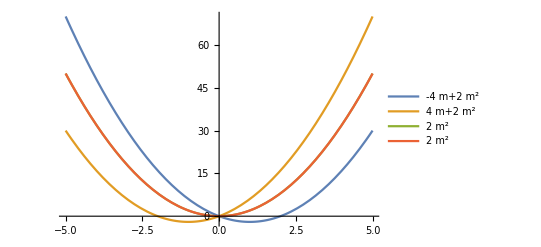

```mathematica
Plot[Evaluate[Normal[{-4 m,4 m,0,0}+2 m^2]],{m, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.1}
```

```mathematica
Eigenvalues[({{-4 m, -0.1, -0.1, -0.1}, {-0.1, 0, -0.1, -0.1}, {-0.1, -0.1, 0, -0.1}, {-0.1, -0.1, -0.1, 4 m}})]
```

{Root[-0.00001875+0.01 m^2+0.0005 #1+(-0.00375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.00001875+0.01 m^2+0.0005 #1+(-0.00375-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.00001875+0.01 m^2+0.0005 #1+(-0.00375-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.00001875+0.01 m^2+0.0005 #1+(-0.00375-1. m^2) #1^2+0.0625 #1^4&,4]}

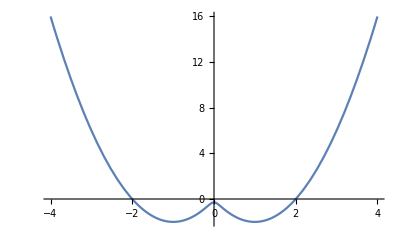

```mathematica
Plot[Evaluate[Normal[{Root[-0.000018750000000000005+0.010000000000000002 m^2+0.0005000000000000001 #1+(-0.0037500000000000007-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.2}
```

```mathematica
Eigenvalues[({{-4 m, -0.2, -0.2, -0.2}, {-0.2, 0, -0.2, -0.2}, {-0.2, -0.2, 0, -0.2}, {-0.2, -0.2, -0.2, 4 m}})]
```

{Root[-0.0003+0.04 m^2+0.004 #1+(-0.015-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.0003+0.04 m^2+0.004 #1+(-0.015-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.0003+0.04 m^2+0.004 #1+(-0.015-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.0003+0.04 m^2+0.004 #1+(-0.015-1. m^2) #1^2+0.0625 #1^4&,4]}

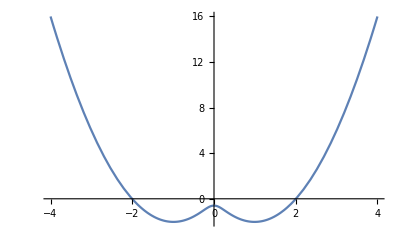

```mathematica
Plot[Evaluate[Normal[{Root[-0.0003000000000000001+0.04000000000000001 m^2+0.004000000000000001 #1+(-0.015000000000000003-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4,4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.5}
```

```mathematica
Eigenvalues[({{-4 m, -0.5, -0.5, -0.5}, {-0.5, 0, -0.5, -0.5}, {-0.5, -0.5, 0, -0.5}, {-0.5, -0.5, -0.5, 4 m}})]
```

{Root[-0.0117188+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.0117188+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.0117188+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.0117188+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,4]}

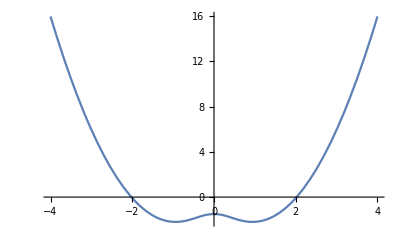

```mathematica
Plot[Evaluate[Normal[{Root[-0.01171875+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.7}
```

```mathematica
Eigenvalues[({{-4 m, -0.7, -0.7, -0.7}, {-0.7, 0, -0.7, -0.7}, {-0.7, -0.7, 0, -0.7}, {-0.7, -0.7, -0.7, 4 m}})]
```

{Root[-0.0450187+0.49 m^2+(0.1715-2.77556×10^-17 m) #1+(-0.18375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.0450187+0.49 m^2+(0.1715-2.77556×10^-17 m) #1+(-0.18375-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.0450187+0.49 m^2+(0.1715-2.77556×10^-17 m) #1+(-0.18375-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.0450187+0.49 m^2+(0.1715-2.77556×10^-17 m) #1+(-0.18375-1. m^2) #1^2+0.0625 #1^4&,4]}

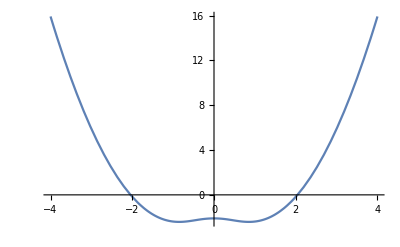

```mathematica
Plot[Evaluate[Normal[{Root[-0.04501874999999998+0.48999999999999994 m^2+(0.17149999999999996-2.7755575615628914*^-17 m) #1+(-0.18374999999999997-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.9}
```

```mathematica
Eigenvalues[({{-4 m, -0.9, -0.9, -0.9}, {-0.9, 0, -0.9, -0.9}, {-0.9, -0.9, 0, -0.9}, {-0.9, -0.9, -0.9, 4 m}})]
```

{Root[-0.123019+0.81 m^2+0.3645 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.123019+0.81 m^2+0.3645 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.123019+0.81 m^2+0.3645 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.123019+0.81 m^2+0.3645 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,4]}

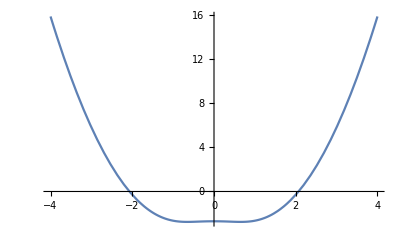

```mathematica
Plot[Evaluate[Normal[{Root[-0.12301875000000002+0.81 m^2+0.36450000000000005 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->1}
```

```mathematica
Eigenvalues[({{-4 m, -1, -1, -1}, {-1, 0, -1, -1}, {-1, -1, 0, -1}, {-1, -1, -1, 4 m}})]
```

{1,Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1],Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,2],Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,3]}

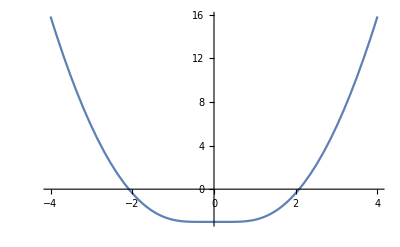

```mathematica
Plot[Evaluate[Normal[{Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->1.2}
```

```mathematica
Eigenvalues[({{-4 m, -1.2, -1.2, -1.2}, {-1.2, 0, -1.2, -1.2}, {-1.2, -1.2, 0, -1.2}, {-1.2, -1.2, -1.2, 4 m}})]
```

{Root[-0.3888+1.44 m^2+(0.864+1.11022×10^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.3888+1.44 m^2+(0.864+1.11022×10^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.3888+1.44 m^2+(0.864+1.11022×10^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.3888+1.44 m^2+(0.864+1.11022×10^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,4]}

```mathematica
Eigenvalues[Ham]/.{ Δ->1.5}
```

```mathematica
Eigenvalues[({{-4 m, -1.5, -1.5, -1.5}, {-1.5, 0, -1.5, -1.5}, {-1.5, -1.5, 0, -1.5}, {-1.5, -1.5, -1.5, 4 m}})]
```

{Root[-0.949219+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.949219+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,2],Root[-0.949219+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,3],Root[-0.949219+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,4]}

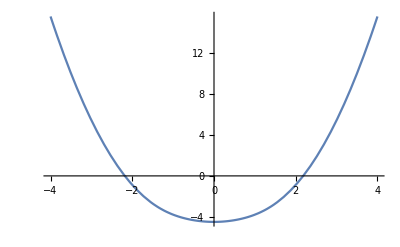

```mathematica
Plot[Evaluate[Normal[{Root[-0.94921875+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

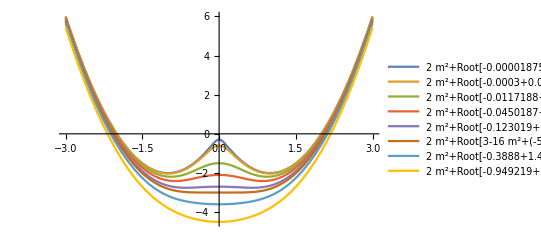

```mathematica
Plot[Evaluate[Normal[{Root[-0.000018750000000000005+0.010000000000000002 m^2+0.0005000000000000001 #1+(-0.0037500000000000007-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.0003000000000000001+0.04000000000000001 m^2+0.004000000000000001 #1+(-0.015000000000000003-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.01171875+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.04501874999999998+0.48999999999999994 m^2+(0.17149999999999996-2.7755575615628914*^-17 m) #1+(-0.18374999999999997-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.12301875000000002+0.81 m^2+0.36450000000000005 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,1],Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1],Root[-0.3888+1.44 m^2+(0.864+1.1102230246251565*^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.94921875+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
H4= -2m(KroneckerProduct[z,I2] + KroneckerProduct[I1,z,I1] + KroneckerProduct[I2,z]) -Δ(KroneckerProduct[x,I2]+ KroneckerProduct[I1,x,I1] + KroneckerProduct[I2,x] + τ KroneckerProduct[x,x,x])//MatrixForm
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ τ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ τ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ τ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ τ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ τ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
Ham = H4/.{τ-> 1}
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
Eigenvalues[Ham]/.{ Δ->0}
```

```mathematica
Eigenvalues[({{-6 m, 0, 0, 0, 0, 0, 0, 0}, {0, -2 m, 0, 0, 0, 0, 0, 0}, {0, 0, -2 m, 0, 0, 0, 0, 0}, {0, 0, 0, 2 m, 0, 0, 0, 0}, {0, 0, 0, 0, -2 m, 0, 0, 0}, {0, 0, 0, 0, 0, 2 m, 0, 0}, {0, 0, 0, 0, 0, 0, 2 m, 0}, {0, 0, 0, 0, 0, 0, 0, 6 m}})]
```

{-6 m,6 m,-2 m,-2 m,-2 m,2 m,2 m,2 m}

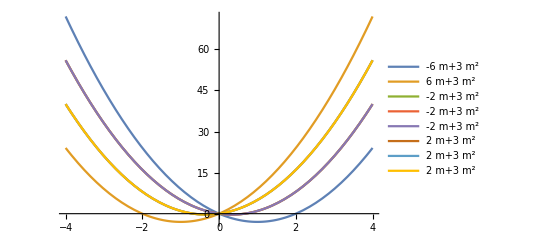

```mathematica
Plot[Evaluate[Normal[{-6 m,6 m,-2 m,-2 m,-2 m,2 m,2 m,2 m}+3 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.1}
```

```mathematica
Eigenvalues[({{-6 m, -0.1, -0.1, 0, -0.1, 0, 0, -0.1}, {-0.1, -2 m, 0, -0.1, 0, -0.1, -0.1, 0}, {-0.1, 0, -2 m, -0.1, 0, -0.1, -0.1, 0}, {0, -0.1, -0.1, 2 m, -0.1, 0, 0, -0.1}, {-0.1, 0, 0, -0.1, -2 m, -0.1, -0.1, 0}, {0, -0.1, -0.1, 0, -0.1, 2 m, 0, -0.1}, {0, -0.1, -0.1, 0, -0.1, 0, 2 m, -0.1}, {-0.1, 0, 0, -0.1, 0, -0.1, -0.1, 6 m}})]
```

{Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,1],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,2],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,3],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,4],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,5],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,6],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,7],Root[4.51751×10^-24 m^2-1.50584×10^-20 m^4+0.0177778 m^6+1. m^8+(6.02335×10^-22 m^3-3.85494×10^-19 m^5) #1+(4.51751×10^-22 m^2-0.01 m^4-0.777778 m^6) #1^2-7.52918×10^-23 m #1^3+(-3.01167×10^-22+0.00166667 m^2+0.208333 m^4) #1^4+1.20467×10^-20 m #1^5+(-0.0000694444-0.0208333 m^2) #1^6+0.000434028 #1^8&,8]}

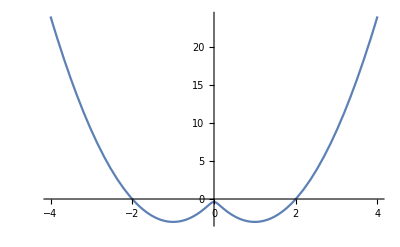

```mathematica
Plot[Evaluate[Normal[{Root[4.5175090520229365*^-24 m^2-1.5058363506743118*^-20 m^4+0.017777777777777778 m^6+1. m^8+(6.023345402697249*^-22 m^3-3.854941057726238*^-19 m^5) #1+(4.517509052022938*^-22 m^2-0.010000000000000002 m^4-0.7777777777777778 m^6) #1^2-7.529181753371559*^-23 m #1^3+(-3.0116727013486235*^-22+0.001666666666666667 m^2+0.20833333333333334 m^4) #1^4+1.2046690805394493*^-20 m #1^5+(-0.00006944444444444444-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.3}
```

```mathematica
Eigenvalues[({{-6 m, -0.3, -0.3, 0, -0.3, 0, 0, -0.3}, {-0.3, -2 m, 0, -0.3, 0, -0.3, -0.3, 0}, {-0.3, 0, -2 m, -0.3, 0, -0.3, -0.3, 0}, {0, -0.3, -0.3, 2 m, -0.3, 0, 0, -0.3}, {-0.3, 0, 0, -0.3, -2 m, -0.3, -0.3, 0}, {0, -0.3, -0.3, 0, -0.3, 2 m, 0, -0.3}, {0, -0.3, -0.3, 0, -0.3, 0, 2 m, -0.3}, {-0.3, 0, 0, -0.3, 0, -0.3, -0.3, 6 m}})]
```

{Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,1],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,2],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,3],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,4],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,5],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,6],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,7],Root[9.75782×10^-22 m^2-5.78241×10^-19 m^4+0.16 m^6+1. m^8+(4.87891×10^-22 m-5.20417×10^-20 m^3-4.62593×10^-18 m^5) #1+(8.31222×10^-20 m^2-0.09 m^4-0.777778 m^6) #1^2+(-3.25261×10^-21 m-7.70988×10^-19 m^3) #1^3+(-1.0842×10^-20+0.015 m^2+0.208333 m^4) #1^4+9.63735×10^-20 m #1^5+(-0.000625-0.0208333 m^2) #1^6+0.000434028 #1^8&,8]}

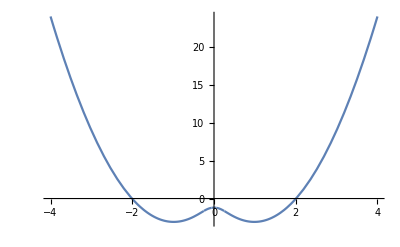

```mathematica
Plot[Evaluate[Normal[{Root[9.757819552369541*^-22 m^2-5.782411586589357*^-19 m^4+0.16 m^6+1. m^8+(4.87890977618477*^-22 m-5.204170427930419*^-20 m^3-4.625929269271485*^-18 m^5) #1+(8.312216655722201*^-20 m^2-0.09 m^4-0.7777777777777778 m^6) #1^2+(-3.2526065174565136*^-21 m-7.709882115452476*^-19 m^3) #1^3+(-1.0842021724855043*^-20+0.015000000000000001 m^2+0.20833333333333334 m^4) #1^4+9.637352644315594*^-20 m #1^5+(-0.0006250000000000001-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -4, 4}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.5}
```

```mathematica
Eigenvalues[({{-6 m, -0.5, -0.5, 0, -0.5, 0, 0, -0.5}, {-0.5, -2 m, 0, -0.5, 0, -0.5, -0.5, 0}, {-0.5, 0, -2 m, -0.5, 0, -0.5, -0.5, 0}, {0, -0.5, -0.5, 2 m, -0.5, 0, 0, -0.5}, {-0.5, 0, 0, -0.5, -2 m, -0.5, -0.5, 0}, {0, -0.5, -0.5, 0, -0.5, 2 m, 0, -0.5}, {0, -0.5, -0.5, 0, -0.5, 0, 2 m, -0.5}, {-0.5, 0, 0, -0.5, 0, -0.5, -0.5, 6 m}})]
```

{Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,1],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,2],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,3],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,4],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,5],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,6],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,7],Root[0.444444 m^6+1. m^8+(-0.25 m^4-0.777778 m^6) #1^2+(0.0416667 m^2+0.208333 m^4) #1^4+(-0.00173611-0.0208333 m^2) #1^6+0.000434028 #1^8&,8]}

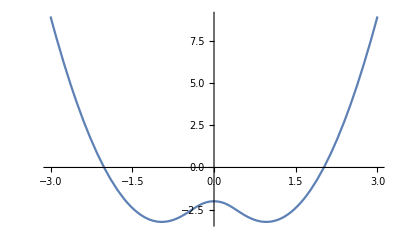

```mathematica
Plot[Evaluate[Normal[{Root[0.4444444444444444 m^6+1. m^8+(-0.25 m^4-0.7777777777777778 m^6) #1^2+(0.041666666666666664 m^2+0.20833333333333334 m^4) #1^4+(-0.001736111111111111-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->0.7}
```

```mathematica
Eigenvalues[({{-6 m, -0.7, -0.7, 0, -0.7, 0, 0, -0.7}, {-0.7, -2 m, 0, -0.7, 0, -0.7, -0.7, 0}, {-0.7, 0, -2 m, -0.7, 0, -0.7, -0.7, 0}, {0, -0.7, -0.7, 2 m, -0.7, 0, 0, -0.7}, {-0.7, 0, 0, -0.7, -2 m, -0.7, -0.7, 0}, {0, -0.7, -0.7, 0, -0.7, 2 m, 0, -0.7}, {0, -0.7, -0.7, 0, -0.7, 0, 2 m, -0.7}, {-0.7, 0, 0, -0.7, 0, -0.7, -0.7, 6 m}})]
```

{Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,1],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,2],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,3],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,4],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,5],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,6],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,7],Root[1.32224×10^-19 m^2-2.15877×10^-18 m^4+0.871111 m^6+1. m^8+(9.25571×10^-20 m-3.07624×10^-18 m^3-1.54198×10^-17 m^5) #1+(-4.04769×10^-19 m^2-0.49 m^4-0.777778 m^6) #1^2+(-1.07938×10^-19 m-4.62593×10^-18 m^3) #1^3+(5.39692×10^-19+0.0816667 m^2+0.208333 m^4) #1^4+1.92747×10^-19 m #1^5+(-0.00340278-0.0208333 m^2) #1^6+0.000434028 #1^8&,8]}

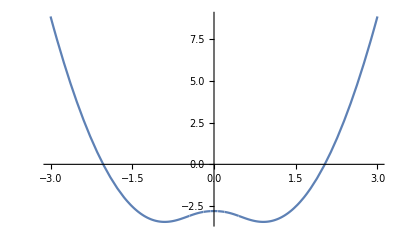

```mathematica
Plot[Evaluate[Normal[{Root[1.3222447828000993*^-19 m^2-2.1587669923266933*^-18 m^4+0.871111111111111 m^6+1. m^8+(9.255713479600694*^-20 m-3.0762429640655373*^-18 m^3-1.5419764230904953*^-17 m^5) #1+(-4.047688110612549*^-19 m^2-0.48999999999999994 m^4-0.7777777777777778 m^6) #1^2+(-1.0793834961633464*^-19 m-4.625929269271485*^-18 m^3) #1^3+(5.396917480816733*^-19+0.08166666666666665 m^2+0.20833333333333334 m^4) #1^4+1.927470528863119*^-19 m #1^5+(-0.003402777777777777-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->1}
```

```mathematica
Eigenvalues[({{-6 m, -1, -1, 0, -1, 0, 0, -1}, {-1, -2 m, 0, -1, 0, -1, -1, 0}, {-1, 0, -2 m, -1, 0, -1, -1, 0}, {0, -1, -1, 2 m, -1, 0, 0, -1}, {-1, 0, 0, -1, -2 m, -1, -1, 0}, {0, -1, -1, 0, -1, 2 m, 0, -1}, {0, -1, -1, 0, -1, 0, 2 m, -1}, {-1, 0, 0, -1, 0, -1, -1, 6 m}})]
```

{-2 m,-2 m,2 m,2 m,-2 √(2+5 m^2-2 √(1+m^2+4 m^4)),2 √(2+5 m^2-2 √(1+m^2+4 m^4)),-2 √(2+5 m^2+2 √(1+m^2+4 m^4)),2 √(2+5 m^2+2 √(1+m^2+4 m^4))}

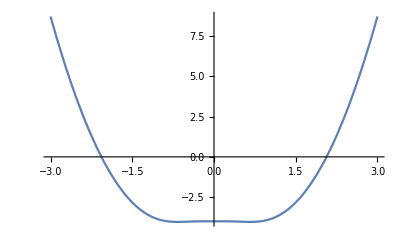

```mathematica
Plot[Evaluate[Normal[{-2 √(2+5 m^2+2 √(1+m^2+4 m^4))}+3 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Eigenvalues[Ham]/.{ Δ->1.2}
```

```mathematica
Eigenvalues[({{-6 m, -1.2, -1.2, 0, -1.2, 0, 0, -1.2}, {-1.2, -2 m, 0, -1.2, 0, -1.2, -1.2, 0}, {-1.2, 0, -2 m, -1.2, 0, -1.2, -1.2, 0}, {0, -1.2, -1.2, 2 m, -1.2, 0, 0, -1.2}, {-1.2, 0, 0, -1.2, -2 m, -1.2, -1.2, 0}, {0, -1.2, -1.2, 0, -1.2, 2 m, 0, -1.2}, {0, -1.2, -1.2, 0, -1.2, 0, 2 m, -1.2}, {-1.2, 0, 0, -1.2, 0, -1.2, -1.2, 6 m}})]
```

{Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,1],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,2],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,3],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,4],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,5],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,6],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,7],Root[3.9968×10^-18 m^2-1.4803×10^-16 m^4+2.56 m^6+1. m^8+(1.9984×10^-18 m-1.33227×10^-17 m^3-7.40149×10^-17 m^5) #1+(2.12793×10^-17 m^2-1.44 m^4-0.777778 m^6) #1^2+(-8.32667×10^-19 m-1.23358×10^-17 m^3) #1^3+(-2.77556×10^-18+0.24 m^2+0.208333 m^4) #1^4+1.54198×10^-18 m #1^5+(-0.01-0.0208333 m^2) #1^6+0.000434028 #1^8&,8]}

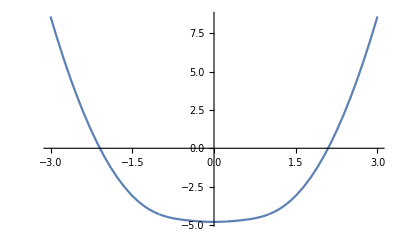

```mathematica
Plot[Evaluate[Normal[{Root[3.996802888650564*^-18 m^2-1.4802973661668753*^-16 m^4+2.56 m^6+1. m^8+(1.9984014443252816*^-18 m-1.3322676295501873*^-17 m^3-7.401486830834377*^-17 m^5) #1+(2.1279274638648835*^-17 m^2-1.44 m^4-0.7777777777777778 m^6) #1^2+(-8.326672684688675*^-19 m-1.2335811384723961*^-17 m^3) #1^3+(-2.775557561562891*^-18+0.24000000000000002 m^2+0.20833333333333334 m^4) #1^4+1.5419764230904951*^-18 m #1^5+(-0.010000000000000002-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

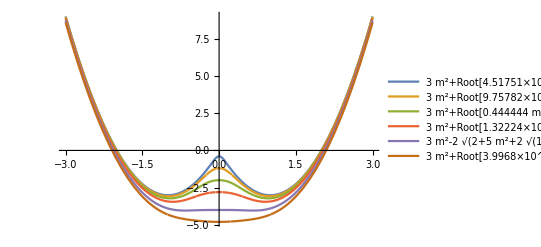

```mathematica
Plot[Evaluate[Normal[{Root[4.5175090520229365*^-24 m^2-1.5058363506743118*^-20 m^4+0.017777777777777778 m^6+1. m^8+(6.023345402697249*^-22 m^3-3.854941057726238*^-19 m^5) #1+(4.517509052022938*^-22 m^2-0.010000000000000002 m^4-0.7777777777777778 m^6) #1^2-7.529181753371559*^-23 m #1^3+(-3.0116727013486235*^-22+0.001666666666666667 m^2+0.20833333333333334 m^4) #1^4+1.2046690805394493*^-20 m #1^5+(-0.00006944444444444444-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[9.757819552369541*^-22 m^2-5.782411586589357*^-19 m^4+0.16 m^6+1. m^8+(4.87890977618477*^-22 m-5.204170427930419*^-20 m^3-4.625929269271485*^-18 m^5) #1+(8.312216655722201*^-20 m^2-0.09 m^4-0.7777777777777778 m^6) #1^2+(-3.2526065174565136*^-21 m-7.709882115452476*^-19 m^3) #1^3+(-1.0842021724855043*^-20+0.015000000000000001 m^2+0.20833333333333334 m^4) #1^4+9.637352644315594*^-20 m #1^5+(-0.0006250000000000001-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[0.4444444444444444 m^6+1. m^8+(-0.25 m^4-0.7777777777777778 m^6) #1^2+(0.041666666666666664 m^2+0.20833333333333334 m^4) #1^4+(-0.001736111111111111-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[1.3222447828000993*^-19 m^2-2.1587669923266933*^-18 m^4+0.871111111111111 m^6+1. m^8+(9.255713479600694*^-20 m-3.0762429640655373*^-18 m^3-1.5419764230904953*^-17 m^5) #1+(-4.047688110612549*^-19 m^2-0.48999999999999994 m^4-0.7777777777777778 m^6) #1^2+(-1.0793834961633464*^-19 m-4.625929269271485*^-18 m^3) #1^3+(5.396917480816733*^-19+0.08166666666666665 m^2+0.20833333333333334 m^4) #1^4+1.927470528863119*^-19 m #1^5+(-0.003402777777777777-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],-2 √(2+5 m^2+2 √(1+m^2+4 m^4)),Root[3.996802888650564*^-18 m^2-1.4802973661668753*^-16 m^4+2.56 m^6+1. m^8+(1.9984014443252816*^-18 m-1.3322676295501873*^-17 m^3-7.401486830834377*^-17 m^5) #1+(2.1279274638648835*^-17 m^2-1.44 m^4-0.7777777777777778 m^6) #1^2+(-8.326672684688675*^-19 m-1.2335811384723961*^-17 m^3) #1^3+(-2.775557561562891*^-18+0.24000000000000002 m^2+0.20833333333333334 m^4) #1^4+1.5419764230904951*^-18 m #1^5+(-0.010000000000000002-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
Series[{Root[3.996802888650564*^-18 m^2-1.4802973661668753*^-16 m^4+2.56 m^6+1. m^8+(1.9984014443252816*^-18 m-1.3322676295501873*^-17 m^3-7.401486830834377*^-17 m^5) #1+(2.1279274638648835*^-17 m^2-1.44 m^4-0.7777777777777778 m^6) #1^2+(-8.326672684688675*^-19 m-1.2335811384723961*^-17 m^3) #1^3+(-2.775557561562891*^-18+0.24000000000000002 m^2+0.20833333333333334 m^4) #1^4+1.5419764230904951*^-18 m #1^5+(-0.010000000000000002-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2,{m,0,8}]
```

Series::icm: Series in m to be combined have unequal expansion points 0 and 0..

{(3 m^2+O[m]^9)+(-4.8-7.548×10^-17 (m+0.)-2.5 (m+0.)^2+2.65351×10^-17 (m+0.)^3-0.434028 (m+0.)^4+6.58987×10^-17 (m+0.)^5+0.602816 (m+0.)^6-8.40734×10^-17 (m+0.)^7+0.0654098 (m+0.)^8+O[m+0.]^9)}

```mathematica
Series[Root[4.5175090520229365*^-24 m^2-1.5058363506743118*^-20 m^4+0.017777777777777778 m^6+1. m^8+(6.023345402697249*^-22 m^3-3.854941057726238*^-19 m^5) #1+(4.517509052022938*^-22 m^2-0.010000000000000002 m^4-0.7777777777777778 m^6) #1^2-7.529181753371559*^-23 m #1^3+(-3.0116727013486235*^-22+0.001666666666666667 m^2+0.20833333333333334 m^4) #1^4+1.2046690805394493*^-20 m #1^5+(-0.00006944444444444444-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],{m,0,8}]
```

-0.4-8.3348×10^-17 (m+0.)-30. (m+0.)^2-6.77626×10^-16 (m+0.)^3-750. (m+0.)^4+2.23532×10^-12 (m+0.)^5+150000. (m+0.)^6-2.17327×10^-10 (m+0.)^7+2.34375×10^6 (m+0.)^8+O[m+0.]^9

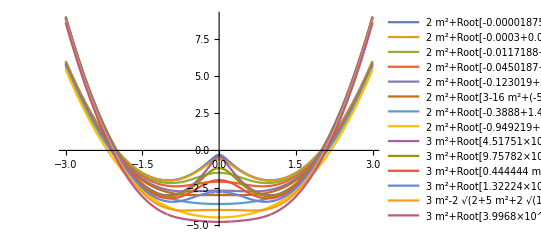

```mathematica
Plot[Evaluate[Normal[{{Root[-0.000018750000000000005+0.010000000000000002 m^2+0.0005000000000000001 #1+(-0.0037500000000000007-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.0003000000000000001+0.04000000000000001 m^2+0.004000000000000001 #1+(-0.015000000000000003-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.01171875+0.25 m^2+0.0625 #1+(-0.09375-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.04501874999999998+0.48999999999999994 m^2+(0.17149999999999996-2.7755575615628914*^-17 m) #1+(-0.18374999999999997-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.12301875000000002+0.81 m^2+0.36450000000000005 #1+(-0.30375-1. m^2) #1^2+0.0625 #1^4&,1],Root[3-16 m^2+(-5-16 m^2) #1+#1^2+#1^3&,1],Root[-0.3888+1.44 m^2+(0.864+1.1102230246251565*^-16 m) #1+(-0.54-1. m^2) #1^2+0.0625 #1^4&,1],Root[-0.94921875+2.25 m^2+1.6875 #1+(-0.84375-1. m^2) #1^2+0.0625 #1^4&,1]}+2 m^2,{Root[4.5175090520229365*^-24 m^2-1.5058363506743118*^-20 m^4+0.017777777777777778 m^6+1. m^8+(6.023345402697249*^-22 m^3-3.854941057726238*^-19 m^5) #1+(4.517509052022938*^-22 m^2-0.010000000000000002 m^4-0.7777777777777778 m^6) #1^2-7.529181753371559*^-23 m #1^3+(-3.0116727013486235*^-22+0.001666666666666667 m^2+0.20833333333333334 m^4) #1^4+1.2046690805394493*^-20 m #1^5+(-0.00006944444444444444-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[9.757819552369541*^-22 m^2-5.782411586589357*^-19 m^4+0.16 m^6+1. m^8+(4.87890977618477*^-22 m-5.204170427930419*^-20 m^3-4.625929269271485*^-18 m^5) #1+(8.312216655722201*^-20 m^2-0.09 m^4-0.7777777777777778 m^6) #1^2+(-3.2526065174565136*^-21 m-7.709882115452476*^-19 m^3) #1^3+(-1.0842021724855043*^-20+0.015000000000000001 m^2+0.20833333333333334 m^4) #1^4+9.637352644315594*^-20 m #1^5+(-0.0006250000000000001-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[0.4444444444444444 m^6+1. m^8+(-0.25 m^4-0.7777777777777778 m^6) #1^2+(0.041666666666666664 m^2+0.20833333333333334 m^4) #1^4+(-0.001736111111111111-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],Root[1.3222447828000993*^-19 m^2-2.1587669923266933*^-18 m^4+0.871111111111111 m^6+1. m^8+(9.255713479600694*^-20 m-3.0762429640655373*^-18 m^3-1.5419764230904953*^-17 m^5) #1+(-4.047688110612549*^-19 m^2-0.48999999999999994 m^4-0.7777777777777778 m^6) #1^2+(-1.0793834961633464*^-19 m-4.625929269271485*^-18 m^3) #1^3+(5.396917480816733*^-19+0.08166666666666665 m^2+0.20833333333333334 m^4) #1^4+1.927470528863119*^-19 m #1^5+(-0.003402777777777777-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1],-2 √(2+5 m^2+2 √(1+m^2+4 m^4)),Root[3.996802888650564*^-18 m^2-1.4802973661668753*^-16 m^4+2.56 m^6+1. m^8+(1.9984014443252816*^-18 m-1.3322676295501873*^-17 m^3-7.401486830834377*^-17 m^5) #1+(2.1279274638648835*^-17 m^2-1.44 m^4-0.7777777777777778 m^6) #1^2+(-8.326672684688675*^-19 m-1.2335811384723961*^-17 m^3) #1^3+(-2.775557561562891*^-18+0.24000000000000002 m^2+0.20833333333333334 m^4) #1^4+1.5419764230904951*^-18 m #1^5+(-0.010000000000000002-0.020833333333333332 m^2) #1^6+0.00043402777777777775 #1^8&,1]}+3 m^2}]],{m, -3, 3}, PlotLegends->"Expressions"]
```

```mathematica
H5= -2m(KroneckerProduct[z,I3] + KroneckerProduct[I1,z,I2] + KroneckerProduct[I2,z,I1] + KroneckerProduct[I3,z]) -Δ(KroneckerProduct[x,I3]+ KroneckerProduct[I1,x,I2] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]+ τ KroneckerProduct[x,x,x,x])
```

{{-8 m,-Δ,-Δ,0,-Δ,0,0,0,-Δ,0,0,0,0,0,0,-Δ τ},{-Δ,-4 m,0,-Δ,0,-Δ,0,0,0,-Δ,0,0,0,0,-Δ τ,0},{-Δ,0,-4 m,-Δ,0,0,-Δ,0,0,0,-Δ,0,0,-Δ τ,0,0},{0,-Δ,-Δ,0,0,0,0,-Δ,0,0,0,-Δ,-Δ τ,0,0,0},{-Δ,0,0,0,-4 m,-Δ,-Δ,0,0,0,0,-Δ τ,-Δ,0,0,0},{0,-Δ,0,0,-Δ,0,0,-Δ,0,0,-Δ τ,0,0,-Δ,0,0},{0,0,-Δ,0,-Δ,0,0,-Δ,0,-Δ τ,0,0,0,0,-Δ,0},{0,0,0,-Δ,0,-Δ,-Δ,4 m,-Δ τ,0,0,0,0,0,0,-Δ},{-Δ,0,0,0,0,0,0,-Δ τ,-4 m,-Δ,-Δ,0,-Δ,0,0,0},{0,-Δ,0,0,0,0,-Δ τ,0,-Δ,0,0,-Δ,0,-Δ,0,0},{0,0,-Δ,0,0,-Δ τ,0,0,-Δ,0,0,-Δ,0,0,-Δ,0},{0,0,0,-Δ,-Δ τ,0,0,0,0,-Δ,-Δ,4 m,0,0,0,-Δ},{0,0,0,-Δ τ,-Δ,0,0,0,-Δ,0,0,0,0,-Δ,-Δ,0},{0,0,-Δ τ,0,0,-Δ,0,0,0,-Δ,0,0,-Δ,4 m,0,-Δ},{0,-Δ τ,0,0,0,0,-Δ,0,0,0,-Δ,0,-Δ,0,4 m,-Δ},{-Δ τ,0,0,0,0,0,0,-Δ,0,0,0,-Δ,0,-Δ,-Δ,8 m}}

```mathematica
Ham = H5/. {τ->1}
```

{{-8 m,-Δ,-Δ,0,-Δ,0,0,0,-Δ,0,0,0,0,0,0,-Δ},{-Δ,-4 m,0,-Δ,0,-Δ,0,0,0,-Δ,0,0,0,0,-Δ,0},{-Δ,0,-4 m,-Δ,0,0,-Δ,0,0,0,-Δ,0,0,-Δ,0,0},{0,-Δ,-Δ,0,0,0,0,-Δ,0,0,0,-Δ,-Δ,0,0,0},{-Δ,0,0,0,-4 m,-Δ,-Δ,0,0,0,0,-Δ,-Δ,0,0,0},{0,-Δ,0,0,-Δ,0,0,-Δ,0,0,-Δ,0,0,-Δ,0,0},{0,0,-Δ,0,-Δ,0,0,-Δ,0,-Δ,0,0,0,0,-Δ,0},{0,0,0,-Δ,0,-Δ,-Δ,4 m,-Δ,0,0,0,0,0,0,-Δ},{-Δ,0,0,0,0,0,0,-Δ,-4 m,-Δ,-Δ,0,-Δ,0,0,0},{0,-Δ,0,0,0,0,-Δ,0,-Δ,0,0,-Δ,0,-Δ,0,0},{0,0,-Δ,0,0,-Δ,0,0,-Δ,0,0,-Δ,0,0,-Δ,0},{0,0,0,-Δ,-Δ,0,0,0,0,-Δ,-Δ,4 m,0,0,0,-Δ},{0,0,0,-Δ,-Δ,0,0,0,-Δ,0,0,0,0,-Δ,-Δ,0},{0,0,-Δ,0,0,-Δ,0,0,0,-Δ,0,0,-Δ,4 m,0,-Δ},{0,-Δ,0,0,0,0,-Δ,0,0,0,-Δ,0,-Δ,0,4 m,-Δ},{-Δ,0,0,0,0,0,0,-Δ,0,0,0,-Δ,0,-Δ,-Δ,8 m}}

```mathematica
dm = Range[-2,2,0.2];
```

```mathematica
mag = Table[{4 m^2+Eigenvalues[Ham,1]}/.{ Δ->0.1}, {m,dm}];//FullSimplify
```

```mathematica
N[mag]
```

{{16.+Eigenvalues[(16. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 8. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 8. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 8. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -8. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 8. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -8. | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -8. | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -8. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -16.),1.]},{12.96+Eigenvalues[(14.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 7.2 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 7.2 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 7.2 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -7.2 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 7.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -7.2 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -7.2 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -7.2 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -14.4),1.]},{10.24+Eigenvalues[(12.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 6.4 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 6.4 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 6.4 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -6.4 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 6.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -6.4 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -6.4 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -6.4 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -12.8),1.]},{7.84+Eigenvalues[(11.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 5.6 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 5.6 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 5.6 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -5.6 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 5.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -5.6 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -5.6 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -5.6 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -11.2),1.]},{5.76+Eigenvalues[(9.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 4.8 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 4.8 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 4.8 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -4.8 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 4.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -4.8 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -4.8 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -4.8 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -9.6),1.]},{4.+Eigenvalues[(8. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 4. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 4. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 4. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -4. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 4. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -4. | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -4. | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -4. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -8.),1.]},{2.56+Eigenvalues[(6.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 3.2 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 3.2 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 3.2 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -3.2 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 3.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -3.2 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -3.2 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -3.2 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -6.4),1.]},{1.44+Eigenvalues[(4.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 2.4 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 2.4 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 2.4 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -2.4 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 2.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -2.4 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -2.4 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -2.4 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -4.8),1.]},{0.64+Eigenvalues[(3.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 1.6 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 1.6 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 1.6 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -1.6 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 1.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -1.6 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -1.6 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -1.6 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -3.2),1.]},{0.16+Eigenvalues[(1.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0.8 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 0.8 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 0.8 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -0.8 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | -0.8 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | -0.8 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | -0.8 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | -1.6),1.]},{0.+Eigenvalues[(0. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 0.),1.]},{0.16+Eigenvalues[(-1.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -0.8 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -0.8 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -0.8 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 0.8 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -0.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.8 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.8 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.8 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 1.6),1.]},{0.64+Eigenvalues[(-3.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -1.6 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -1.6 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -1.6 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 1.6 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -1.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 1.6 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 1.6 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 1.6 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 3.2),1.]},{1.44+Eigenvalues[(-4.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -2.4 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -2.4 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -2.4 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 2.4 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -2.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 2.4 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 2.4 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 2.4 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 4.8),1.]},{2.56+Eigenvalues[(-6.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -3.2 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -3.2 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -3.2 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 3.2 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -3.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 3.2 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 3.2 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 3.2 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 6.4),1.]},{4.+Eigenvalues[(-8. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -4. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -4. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -4. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 4. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -4. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 4. | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 4. | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 4. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 8.),1.]},{5.76+Eigenvalues[(-9.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -4.8 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -4.8 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -4.8 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 4.8 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -4.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 4.8 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 4.8 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 4.8 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 9.6),1.]},{7.84+Eigenvalues[(-11.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -5.6 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -5.6 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -5.6 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 5.6 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -5.6 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 5.6 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 5.6 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 5.6 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 11.2),1.]},{10.24+Eigenvalues[(-12.8 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -6.4 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -6.4 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -6.4 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 6.4 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -6.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 6.4 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 6.4 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 6.4 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 12.8),1.]},{12.96+Eigenvalues[(-14.4 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -7.2 | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -7.2 | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -7.2 | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 7.2 | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -7.2 | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 7.2 | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 7.2 | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 7.2 | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 14.4),1.]},{16.+Eigenvalues[(-16. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | -8. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
-0.1 | 0. | -8. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
-0.1 | 0. | 0. | 0. | -8. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 8. | -0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | -8. | -0.1 | -0.1 | 0. | -0.1 | 0. | 0. | 0.
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 0.
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 8. | 0. | 0. | 0. | -0.1
0. | 0. | 0. | -0.1 | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | -0.1 | 0.
0. | 0. | -0.1 | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | 0. | -0.1 | 8. | 0. | -0.1
0. | -0.1 | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | 0. | 8. | -0.1
-0.1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.1 | 0. | 0. | 0. | -0.1 | 0. | -0.1 | -0.1 | 16.),1.]}}

```mathematica
{{16.+Eigenvalues[({{16., -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 8., 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 8., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 8., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -8., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 8., -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -8., 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -8., 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -8., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -16.}}),1.]},{12.96+Eigenvalues[({{14.4, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 7.2, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 7.2, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 7.2, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -7.2, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 7.2, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -7.2, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -7.2, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -7.2, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -14.4}}),1.]},{10.240000000000002+Eigenvalues[({{12.8, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 6.4, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 6.4, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 6.4, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -6.4, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 6.4, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -6.4, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -6.4, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -6.4, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -12.8}}),1.]},{7.839999999999999+Eigenvalues[({{11.2, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 5.6, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 5.6, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 5.6, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -5.6, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 5.6, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -5.6, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -5.6, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -5.6, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -11.2}}),1.]},{5.76+Eigenvalues[({{9.6, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 4.8, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 4.8, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 4.8, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -4.8, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 4.8, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -4.8, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -4.8, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -4.8, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -9.6}}),1.]},{4.+Eigenvalues[({{8., -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 4., 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 4., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 4., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -4., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 4., -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -4., 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -4., 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -4., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -8.}}),1.]},{2.5599999999999987+Eigenvalues[({{6.399999999999999, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 3.1999999999999993, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 3.1999999999999993, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 3.1999999999999993, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -3.1999999999999993, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 3.1999999999999993, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -3.1999999999999993, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -3.1999999999999993, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -3.1999999999999993, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -6.399999999999999}}),1.]},{1.4399999999999993+Eigenvalues[({{4.799999999999999, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 2.3999999999999995, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 2.3999999999999995, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 2.3999999999999995, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -2.3999999999999995, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 2.3999999999999995, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -2.3999999999999995, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -2.3999999999999995, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -2.3999999999999995, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -4.799999999999999}}),1.]},{0.6399999999999997+Eigenvalues[({{3.1999999999999993, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 1.5999999999999996, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 1.5999999999999996, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 1.5999999999999996, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -1.5999999999999996, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 1.5999999999999996, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -1.5999999999999996, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -1.5999999999999996, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -1.5999999999999996, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -3.1999999999999993}}),1.]},{0.15999999999999992+Eigenvalues[({{1.5999999999999996, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0.7999999999999998, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 0.7999999999999998, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 0.7999999999999998, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, -0.7999999999999998, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0.7999999999999998, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, -0.7999999999999998, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, -0.7999999999999998, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., -0.7999999999999998, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, -1.5999999999999996}}),1.]},{0.+Eigenvalues[({{0., -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 0.}}),1.]},{0.16000000000000028+Eigenvalues[({{-1.6000000000000014, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -0.8000000000000007, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -0.8000000000000007, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -0.8000000000000007, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 0.8000000000000007, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -0.8000000000000007, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.8000000000000007, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0.8000000000000007, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 0.8000000000000007, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 1.6000000000000014}}),1.]},{0.6400000000000011+Eigenvalues[({{-3.200000000000003, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -1.6000000000000014, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -1.6000000000000014, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -1.6000000000000014, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 1.6000000000000014, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -1.6000000000000014, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 1.6000000000000014, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 1.6000000000000014, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 1.6000000000000014, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 3.200000000000003}}),1.]},{1.4400000000000004+Eigenvalues[({{-4.800000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -2.4000000000000004, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -2.4000000000000004, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -2.4000000000000004, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 2.4000000000000004, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -2.4000000000000004, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 2.4000000000000004, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 2.4000000000000004, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 2.4000000000000004, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 4.800000000000001}}),1.]},{2.560000000000002+Eigenvalues[({{-6.400000000000002, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -3.200000000000001, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -3.200000000000001, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -3.200000000000001, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 3.200000000000001, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -3.200000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 3.200000000000001, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 3.200000000000001, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 3.200000000000001, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 6.400000000000002}}),1.]},{4.+Eigenvalues[({{-8., -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -4., 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -4., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -4., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 4., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -4., -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 4., 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 4., 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 4., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 8.}}),1.]},{5.760000000000002+Eigenvalues[({{-9.600000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -4.800000000000001, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -4.800000000000001, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -4.800000000000001, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 4.800000000000001, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -4.800000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 4.800000000000001, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 4.800000000000001, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 4.800000000000001, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 9.600000000000001}}),1.]},{7.840000000000004+Eigenvalues[({{-11.200000000000003, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -5.600000000000001, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -5.600000000000001, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -5.600000000000001, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 5.600000000000001, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -5.600000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 5.600000000000001, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 5.600000000000001, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 5.600000000000001, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 11.200000000000003}}),1.]},{10.240000000000002+Eigenvalues[({{-12.8, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -6.4, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -6.4, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -6.4, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 6.4, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -6.4, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 6.4, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 6.4, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 6.4, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 12.8}}),1.]},{12.960000000000004+Eigenvalues[({{-14.400000000000002, -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -7.200000000000001, 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -7.200000000000001, -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -7.200000000000001, -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 7.200000000000001, -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -7.200000000000001, -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 7.200000000000001, 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 7.200000000000001, 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 7.200000000000001, -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 14.400000000000002}}),1.]},{16.+Eigenvalues[({{-16., -0.1, -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, -8., 0., -0.1, 0., -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {-0.1, 0., -8., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., -0.1, -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {-0.1, 0., 0., 0., -8., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0., 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, 0., -0.1, -0.1, 8., -0.1, 0., 0., 0., 0., 0., 0., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, -8., -0.1, -0.1, 0., -0.1, 0., 0., 0.}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., -0.1, 0., 0., -0.1, 0., -0.1, 0., 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0., 0., -0.1, 0.}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., 0., -0.1, -0.1, 8., 0., 0., 0., -0.1}, {0., 0., 0., -0.1, -0.1, 0., 0., 0., -0.1, 0., 0., 0., 0., -0.1, -0.1, 0.}, {0., 0., -0.1, 0., 0., -0.1, 0., 0., 0., -0.1, 0., 0., -0.1, 8., 0., -0.1}, {0., -0.1, 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, 0., 8., -0.1}, {-0.1, 0., 0., 0., 0., 0., 0., -0.1, 0., 0., 0., -0.1, 0., -0.1, -0.1, 16.}}),1.]}}
```

{{{-0.00531192}},{{-1.4459}},{{-2.56664}},{{-3.36759}},{{-3.84885}},{{-4.01062}},{{-3.85327}},{{-3.37769}},{{-2.58651}},{{-1.49288}},{{-0.5}},{{-1.49288}},{{-2.58651}},{{-3.37769}},{{-3.85327}},{{-4.01062}},{{-3.84885}},{{-3.36759}},{{-2.56664}},{{-1.4459}},{{-0.00531192}}}

```mathematica
magc = {-4.010620658892076,-3.9717996973796605,-3.853273081028881,-3.655166707416538,-3.377690190606305,-3.02122032674637,-2.5865094035038374,-2.0753094828516354,-1.4928792240259374,-0.8660629328384855,-0.5000000000000002,-0.8660629328384859,-1.4928792240259383,-2.075309482851636,-2.5865094035038374,-3.021220326746368,-3.3776901906063035,-3.655166707416541,-3.853273081028888,-3.971799697379665,-4.010620658892073}
```

{-4.01062,-3.9718,-3.85327,-3.65517,-3.37769,-3.02122,-2.58651,-2.07531,-1.49288,-0.866063,-0.5,-0.866063,-1.49288,-2.07531,-2.58651,-3.02122,-3.37769,-3.65517,-3.85327,-3.9718,-4.01062}

```mathematica
magc1={-0.005311917762163887,-1.4459019851201038,-2.566639507119355,-3.36758763764803,-3.8488515932684066,-4.010620658892076,-3.8532730810288847,-3.3776901906063035,-2.5865094035038374,-1.4928792240259374,-0.5000000000000002,-1.4928792240259383,-2.586509403503841,-3.3776901906063035,-3.8532730810288895,-4.010620658892073,-3.848851593268405,-3.3675876376480245,-2.5666395071193673,-1.4459019851200896,-0.005311917762153229}
```

{-0.00531192,-1.4459,-2.56664,-3.36759,-3.84885,-4.01062,-3.85327,-3.37769,-2.58651,-1.49288,-0.5,-1.49288,-2.58651,-3.37769,-3.85327,-4.01062,-3.84885,-3.36759,-2.56664,-1.4459,-0.00531192}

```mathematica
dm
```

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

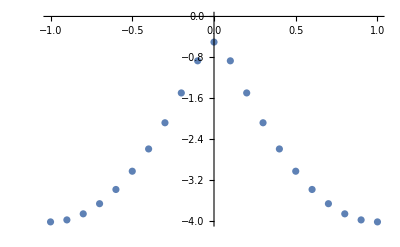

```mathematica
ListPlot[Table[{dm[[t]],magc[[t]]},{t,1,Length[dm],1}]]
```

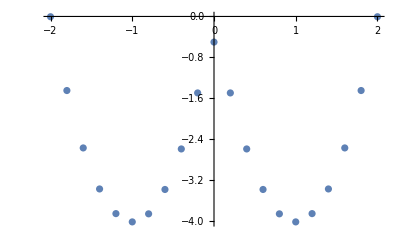

```mathematica
ListPlot[Table[{dm[[t]],magc1[[t]]},{t,1,Length[dm],1}]]
```

```mathematica
dm := Range[-1,1, .01]
```

```mathematica
mag1 = Flatten[Table[4 m^2+Eigenvalues[Ham,1],{Δ,0.9,1.2,0.01},{m,dm}][[1,All]]]//FullSimplify;
```

```mathematica
mag2 = Flatten[Table[4 m^2+Eigenvalues[Ham,1],{Δ,0.9,1.2,0.01},{m,dm}][[15,All]]]//FullSimplify;
```

```mathematica
mag3 = Flatten[Table[4 m^2+Eigenvalues[Ham,1],{Δ,0.9,1.2,0.01},{m,dm}][[18,All]]]//FullSimplify;
```

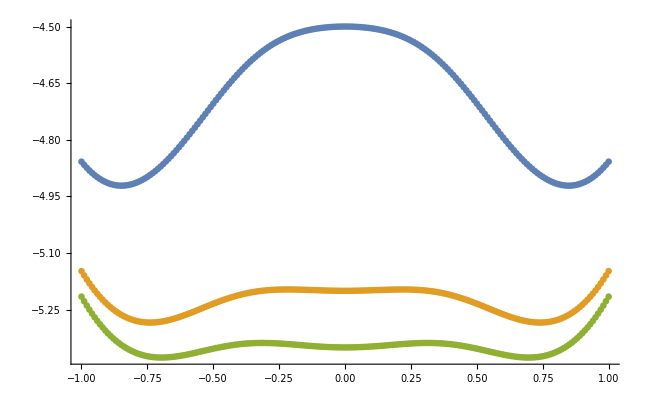

```mathematica
ListPlot[{Thread[{dm, mag1}],Thread[{dm, mag2}],Thread[{dm, mag3}]},AxesLabel->Automatic]
```